```mathematica
f[T_]:=Sqrt[(m/(2 π k T))^3]4 π v^2 Exp[-(m v^2)/(2 k T)]
```

```mathematica
m=2.18017137×10^-25;
k=1.3806488 10^-23;
```

```mathematica
k=8.617 10^-5
```

0.00008617

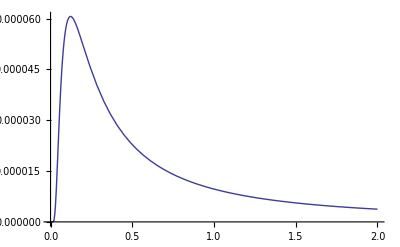

```mathematica
Plot[(f[T])/.v->15250,{T,0,20000000},PlotRange->Full]
```

```mathematica
a=Integrate[f[T],T]/.v->15250
```

368206. (0.-0.00130803 √(1/T^3) T^(3/2) Erf[1355.06/(√T)])

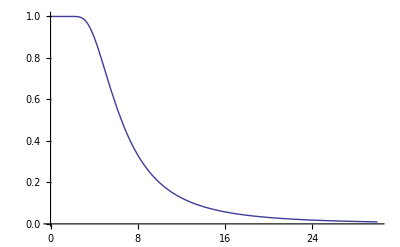

```mathematica
Plot[CDF[MaxwellDistribution[0.1],1/x],{x,0,30},PlotRange->All]
```

```mathematica
maxwell[e_]:=2Sqrt[e/π](1/(k T))^(3/2)Exp[-e/(k T)]
```

```mathematica
a=Integrate[maxwell[e]/.T->1.446 10^6,e]
```

1.26496×10^25 (-1.99642×10^-17 √e ⅇ^(-5.00897×10^16 e)+7.90537×10^-26 Erf[2.23807×10^8 √e])

```mathematica
a=(-5000 ⅇ^(-x^2/10000) x+250000 √π Erf[x/100])/1000000
```

(-5000 ⅇ^(-x^2/10000) x+250000 √π Erf[x/100])/1000000

```mathematica
k=1
```

1

```mathematica
maxwell[100]/.T->1.446 10^6
```

0.00363599

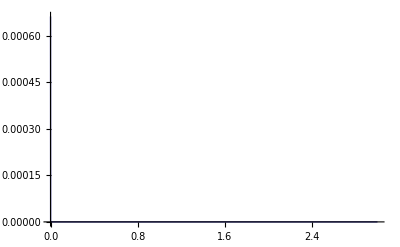

```mathematica
Plot[maxwell[e]/.T->1.4 10^6,{e,0,30000000},PlotRange->All]
```

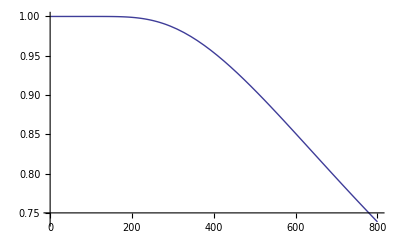

```mathematica
Plot[1+NIntegrate[maxwell[e]/.T->0.5,{e,800,800/x}],{x,1,800},PlotRange->Full]
```

```mathematica
u[x_]:=k (q1 q2)/x;
```

```mathematica
a=FullSimplify[ Convolve[f[x]/.v->15250,u[x]/.{q1->-10, q2->1},x,y]]
```

(0.+1.59707×10^-16 ⅈ) ⅇ^(-(1.83619×10^6+2.24868×10^-10 ⅈ)/y) (1/y)^(3/2)-(0.+4.07166×10^-36 ⅈ)/y-(1.59707×10^-16+0. ⅈ) ⅇ^(-(1.83619×10^6+2.24868×10^-10 ⅈ)/y) (1/y)^(3/2) Erfi[(1355.06+8.29735×10^-14 ⅈ) √(1/y)]+(ⅇ^(-1.83619×10^6/y) ((0.+1.59707×10^-16 ⅈ)+1.59707×10^-16 Erfi[(1355.06+0. ⅈ)/(√y)]))/y^(3/2)

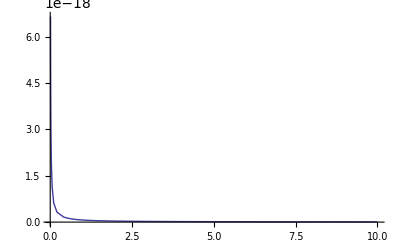

```mathematica
Plot[N[a,100],{y,0.01,10},PlotRange->Full]
```

```mathematica
Plot[Convolve[u[x]/.{q1->-1, q2->1},maxwell[x],x,y],{y,0,10}]
```

$Aborted

```mathematica
ϵ=8.854 10^-12
```

8.854×10^-12

```mathematica
R[t_]:=61 10^-9+2 15250*t;(*meter*)
```

```mathematica
V[t_,q_]:=q/(4 π ϵ R[t]); (*in volt*)
```

```mathematica
V[0,250000]
```

3.6835×10^22

```mathematica
V[800 10^-15,10^6]
```

19645.3

```mathematica
2 15250
```

30500

```mathematica
V[400 10^-15,10^8]
```

2.14313×10^6

```mathematica
250*0.8
```

200.